Dynamic simulation of three-wheeled omnidirectional mobile robot

```mathematica
NotebookSave[]
```

```mathematica
Clear["Global`*"];
```

## Basic definitions

### Configuration definition

#### Global coordinate system definition

```mathematica
ux={1,0,0};
uy={0,1,0};
uz={0,0,1};
rO={0,0,0};
```

#### Basic coordinate system definition

```mathematica
φA=π/6; φB=φA+(2π)/3;φC=φB+(2π)/3;
```

```mathematica
uxA=RotationMatrix[φA,{0,0,1}].ux;
uxB=RotationMatrix[φB,{0,0,1}].ux;
uxC=RotationMatrix[φC,{0,0,1}].ux;
uyA=RotationMatrix[φA,{0,0,1}].uy;
uyB=RotationMatrix[φB,{0,0,1}].uy;
uyC=RotationMatrix[φC,{0,0,1}].uy;
uzA=Cross[uxA,uyA];
uzB=Cross[uxB,uyB];
uzC=Cross[uxC,uyC];
```

#### Wheel definition

```mathematica
wheelCircleRadius=0.12;
wheelRadius=0.03;
wheelWidth=0.0050;
massWheel=0.06;
A=({{-Sin[φA], Cos[φA], wheelCircleRadius}, {-Sin[φB], Cos[φB], wheelCircleRadius}, {-Sin[φC], Cos[φC], wheelCircleRadius}});
```

```mathematica
rA=wheelCircleRadius uxA;
rB=wheelCircleRadius uxB;
rC=wheelCircleRadius uxC;
wheelθMeasured = 0.012099670934420;
```

#### Case definition

```mathematica
ρ=1000;
mTriangleCase = 0.184;
mMotor =0.200;
mWheel =0.060;
mOthers =1.543-3×(mWheel+mMotor)-2×mTriangleCase
offsetLength1=0.04;
offsetLength2= offsetLength1+0.05;
wheelCircleRadiusRatio =0.8;
dummyCaseRadius=wheelCircleRadiusRatio wheelCircleRadius;
dummyCaseHeight=0.05;
r1={0,0,offsetLength1};
r2={0,0,offsetLength2};
CaseCenterOfMassCalc[mTriangleCase_,mMotor_,mOthers_]:=Module[{mCase,cmCase},
mCase=2×mTriangleCase +3×mMotor+mOthers;
cmCase = (mTriangleCase( r1 + r2)+3×mMotor rO+ (r1 + r2 )mOthers)/mCase;
{mCase,cmCase}
]
```

0.395

```mathematica
CaseCenterOfMassCalc[mTriangleCase,mMotor,mOthers]
```

{1.363,{0.,0.,0.0552238}}

#### Package definition

Simple package

```mathematica
ρ=2500;
packageHeight = 0.1;
packageRadius=0.5 dummyCaseRadius;
cmPackage=r2+{0,0,packageHeight/2};
mPackage=packageRadius^2 π packageHeight ρ
```

1.80956

Rod

```mathematica
ρ=7800;rodHeight = 1; rodDiameter = 0.010;
```

```mathematica
RodCenterOfMassCalc[rodHeight_]:=Module[{mRod,cmRod},
mRod=(rodDiameter/2)^2 π rodHeight ρ;mRod=.373;
cmRod=r2+{0,0,rodHeight/2};
{mRod,cmRod}
]
```

```mathematica
RodCenterOfMassCalc[rodHeight]
```

{0.373,{0,0,0.59}}

Disk

```mathematica
ρ=6500;diskHeight = 0.01; diskDiameter = 0.100;mDisk=(diskDiameter/2)^2 π diskHeight ρ;mDisk=0.50;rodHeightPercent=.5;
```

```mathematica
DiskCenterOfMassCalc[rodHeight_,rodHeightPercent_]:=Module[{cmDisk},cmDisk=r2+{0,0,rodHeight rodHeightPercent}]
```

```mathematica
DiskCenterOfMassCalc[rodHeight,rodHeightPercent]
```

{0,0,0.59}

#### Common mass center

```mathematica
CommonCenterOfMassCalc[mode_,mOthers_,mPackage_,mDisk_,rodHeight_,rodHeightPercent_]:=Module[{mCase,cmCase,mRod,cmRod,cmDisk,cmC},
{mCase,cmCase}=CaseCenterOfMassCalc[mTriangleCase,mMotor,mOthers];
{mRod,cmRod}=RodCenterOfMassCalc[rodHeight];
cmDisk=DiskCenterOfMassCalc[rodHeight,rodHeightPercent];
Switch[mode,
"Case",cmC=cmCase,
"Package",cmC=(cmCase mCase+cmPackage mPackage)/(mCase+mPackage),
"Disk",cmC=(cmCase mCase+cmRod mRod+cmDisk mDisk)/(mCase+mRod+mDisk)];
cmC
]
```

```mathematica
cmC=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent]
```

{0.,0.,0.264016}

#### Inertias

```mathematica
CalculateInertias[mode_,mOthers_,mPackage_,mDisk_,rodHeight_,rodHeightPercent_]:=
Module[{mCase,cmCase,mRod,cmRod,cmDisk,cmC,xCS,yCS,zCS,θTriangle,θTriangle1,θTriangle2,θCase,θPackage,θRod,θDisk,θMotorA,θMotorB,θMotorC,θMotors,θRobot,mRobot},
{mCase,cmCase}=CaseCenterOfMassCalc[mTriangleCase,mMotor,mOthers];
{mRod,cmRod}=RodCenterOfMassCalc[rodHeight];
cmDisk=DiskCenterOfMassCalc[rodHeight,rodHeightPercent];
cmC=CommonCenterOfMassCalc[mode,mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
θTriangle = ({{1/4 mTriangleCase wheelCircleRadius^2+1/12 mTriangleCase dummyCaseHeight^2, 0, 0}, {0, 1/4 mTriangleCase wheelCircleRadius^2+1/12 mTriangleCase dummyCaseHeight^2, 0}, {0, 0, (mTriangleCase wheelCircleRadius^2)/3}});
{xCS,yCS,zCS}=cmC-r1;
θTriangle1=θTriangle+mTriangleCase ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
{xCS,yCS,zCS}=cmC-r2;
θTriangle2=θTriangle+mTriangleCase ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
θCase = θTriangle1+θTriangle2 ;
{xCS,yCS,zCS}=cmC-cmPackage;
θPackage=({{1/4 mPackage dummyCaseRadius^2+1/12 mPackage dummyCaseHeight^2, 0, 0}, {0, 1/4 mPackage dummyCaseRadius^2+1/12 mPackage dummyCaseHeight^2, 0}, {0, 0, 1/2 mPackage dummyCaseRadius^2}})+mPackage  ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
{xCS,yCS,zCS}=cmC-cmRod;
θRod=({{1/4 mRod (rodDiameter/2)^2+1/12 mRod rodHeight^2, 0, 0}, {0, 1/4 mRod (rodDiameter/2)^2+1/12 mRod rodHeight^2, 0}, {0, 0, 1/2 mRod (rodDiameter/2)^2}})+mRod  ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
{xCS,yCS,zCS}=cmC-cmDisk;
θDisk=({{1/4 mDisk (diskDiameter/2)^2+1/12 mDisk diskHeight^2, 0, 0}, {0, 1/4 mDisk (diskDiameter/2)^2+1/12 mDisk diskHeight^2, 0}, {0, 0, 1/2 mDisk (diskDiameter/2)^2}})+mDisk  ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
{xCS,yCS,zCS}=cmC-rA;
θMotorA = mMotor ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
{xCS,yCS,zCS}=cmC-rB;
θMotorB = mMotor ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
{xCS,yCS,zCS}=cmC-rC;
θMotorC = mMotor ({{yCS^2+zCS^2, -xCS yCS, -xCS zCS}, {-yCS xCS, xCS^2+zCS^2, -yCS zCS}, {-zCS xCS, -zCS yCS, xCS^2+yCS^2}});
θMotors = θMotorA+θMotorB+θMotorC;
Switch[mode,
"Case",θRobot=θCase,
"Package",θRobot=θCase+θPackage,
"Disk",θRobot=θCase+θRod+θDisk];
Switch[mode,
"Case",mRobot=mCase,
"Package",mRobot=mCase+mPackage,
"Disk",mRobot=mCase+mRod+mDisk];
{mRobot,θRobot}
]
```

```mathematica
CalculateInertias["Case",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent]
```

{1.363,{{0.00166664,0.,0.},{0.,0.00166664,0.},{0.,0.,0.0017664}}}

### 3 D model of the robot and its environment

#### Draw functions

```mathematica
TranslateAndRotate[g_,x_,y_,α_]:=Module[{},Rotate[Translate[g,{x,y}],α,{x,y}]]
```

```mathematica
textOffset = 0.02;fontSize=16;
RobotCaseGraphics3D={
Red,
	Sphere[rO,wheelCircleRadius/50],Text[Style["r_O",FontSize->fontSize],rO - ux textOffset],
	Sphere[r1,wheelCircleRadius/50],Text[Style["r_1",FontSize->fontSize],r1 + ux textOffset+ uz textOffset],
	Sphere[r2,wheelCircleRadius/50],Text[Style["r_2",FontSize->fontSize],r2 + ux textOffset+ uz textOffset],
	Sphere[rA,wheelCircleRadius/50],Text[Style["r_A",FontSize->fontSize],rA - ux textOffset],
	Sphere[rB,wheelCircleRadius/50],Text[Style["r_B",FontSize->fontSize],rB - ux textOffset],
	Sphere[rC,wheelCircleRadius/50],Text[Style["r_C",FontSize->fontSize],rC - ux textOffset],
Gray,Opacity[0.7],
	Sphere[rA,wheelCircleRadius/20],
	Sphere[rB,wheelCircleRadius/20],
	Sphere[rC,wheelCircleRadius/20],
Black,Opacity[1],
Text[Style["m_(motor, C)",FontSize->fontSize],rC + 2 ux textOffset],
Text[Style["m_(motor, A)",FontSize->fontSize],rA + 2 ux textOffset],
Text[Style["m_(motor, B)",FontSize->fontSize],rB + 2 ux textOffset],
Black,
	(*Sphere[cmCase,wheelCircleRadius/50],*)(*Text[Style["cmCase",FontSize->fontSize],cmCase - ux textOffset],*)
	(*Sphere[cmPackage,wheelCircleRadius/50],*)(*Text[Style["cmPackage",FontSize->fontSize],cmPackage - ux textOffset],*)
	Sphere[cmC,wheelCircleRadius/50],Text[Style["CoM",FontSize->fontSize],cmC - ux textOffset],
Gray,Opacity[0.1],
	Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
	Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
	Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
Black,Thick,Opacity[1],
	(*Line[{wheelCircleRadiusRatio rA,rA}],*)
	Line[{ rA, rA+offsetLength1 uz}],Line[{rA+offsetLength1 uz, rB+offsetLength1 uz}],
	Line[{ rB, rB+offsetLength1 uz}],Line[{rB+offsetLength1 uz, rC+offsetLength1 uz}],
	Line[{ rC, rC+offsetLength1 uz}],Line[{rC+offsetLength1 uz, rA+offsetLength1 uz}],
	Line[{ rA+offsetLength1 uz, rA+offsetLength2 uz}],Line[{rA+offsetLength2 uz, rB+offsetLength2 uz}],
	Line[{ rB+offsetLength1 uz, rB+offsetLength2 uz}],Line[{rB+offsetLength2 uz, rC+offsetLength2 uz}],
	Line[{ rC+offsetLength1 uz, rC+offsetLength2 uz}],Line[{rC+offsetLength2 uz, rA+offsetLength2 uz}],
Black,Opacity[0.2],Triangle[{rA+offsetLength1 uz,rB+offsetLength1 uz,rC+offsetLength1 uz}],
Black,Opacity[0.2],Triangle[{rA+offsetLength2 uz,rB+offsetLength2 uz,rC+offsetLength2 uz}],
(*Cyan,Opacity[0.6],
Cylinder[{r1,r1+dummyCaseHeight uz},dummyCaseRadius],*),
Brown,Opacity[0.2],EdgeForm[White],
Cylinder[{r2,r2+rodHeight uz},rodDiameter/2],
Cylinder[{r2+rodHeight/2 uz-diskHeight/2 uz,r2+rodHeight/2 uz+diskHeight/2 uz},diskDiameter/2]
};
```

```mathematica
DrawRobot3D[{x_,y_,z_,α_}]:={EdgeForm[Black],Rotate[Translate[RobotCaseGraphics3D,{x,y,z}],α,{0,0,1}]}
```

```mathematica
DrawGround={EdgeForm[Black],
planeSize=20 wheelCircleRadius;
Black,Opacity[0.1],Polygon[{{-planeSize wheelCircleRadius,-planeSize wheelCircleRadius,-wheelRadius},{-planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,-planeSize  wheelCircleRadius,-wheelRadius}}]
};
```

```mathematica
DrawGlobalAxes[{x_,y_,z_,φ_}]:={EdgeForm[Black],
Translate[
{
Black,
	Line[{rO,ux planeSize/13}],Text[Style["x",FontSize->fontSize],1.2ux planeSize/13],
	Line[{rO,uy planeSize/13}],Text[Style["y",FontSize->fontSize],1.2uy planeSize/13],
	Line[{rO,uz planeSize/12}],Text[Style["z",FontSize->fontSize],1.1uz planeSize/12],

},{x,y,z}]}
```

#### Draw 3D graphics

```mathematica
DrawRobot3D[{0,0,0,π/9}]//Graphics3D
```

-Graphics3D-

```mathematica
initialPos={0,0,0,0};
Graphics3D[
DrawRobot3D[initialPos]~Join~DrawGlobalAxes[initialPos]~Join~DrawGround,Boxed->False]
```

-Graphics3D-

### Draw functions

#### DrawRobot

```mathematica
fontSize = 16;
aVectorEnd = 0.3 wheelCircleRadius; aVectorText = 0.35 wheelCircleRadius; 
ϵVectorEnd = 0.3 wheelCircleRadius; ϵVectorText = 0.35 wheelCircleRadius; 
GVectorEnd= 0.45 wheelCircleRadius;GVectorText= 0.47 wheelCircleRadius;
KVectorEnd= 0.3 wheelCircleRadius;KVectorText= 0.35 wheelCircleRadius;
wheelPositionText = 0.01;
vThick=wheelCircleRadius/20;
vArrHead=0.18 wheelCircleRadius;
axisLength=wheelCircleRadius 0.4;
DrawCaseFBD={
Red,Sphere[rO,wheelCircleRadius/100],
Gray,Thickness[vThick/5],Arrowheads[vArrHead],
	Line[{rO,ux axisLength}],Text[Style[x,FontSize->fontSize],1.1ux axisLength],
	Line[{rO,uy axisLength}],Text[Style[y,FontSize->fontSize],1.1uy axisLength],
	Line[{rO,uz axisLength}],Text[Style[z,FontSize->fontSize],1.1uz axisLength],
Black,Thick,Opacity[1],
	(*Line[{wheelCircleRadiusRatio rA,rA}],*)
	Line[{ rA, rA+offsetLength1 uz}],Line[{rA+offsetLength1 uz, rB+offsetLength1 uz}],
	Line[{ rB, rB+offsetLength1 uz}],Line[{rB+offsetLength1 uz, rC+offsetLength1 uz}],
	Line[{ rC, rC+offsetLength1 uz}],Line[{rC+offsetLength1 uz, rA+offsetLength1 uz}],
	Line[{ rA+offsetLength1 uz, rA+offsetLength2 uz}],Line[{rA+offsetLength2 uz, rB+offsetLength2 uz}],
	Line[{ rB+offsetLength1 uz, rB+offsetLength2 uz}],Line[{rB+offsetLength2 uz, rC+offsetLength2 uz}],
	Line[{ rC+offsetLength1 uz, rC+offsetLength2 uz}],Line[{rC+offsetLength2 uz, rA+offsetLength2 uz}],
Blue,Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{cmC,cmC-GVectorEnd uz}],Text[Style["G",FontSize->16],cmC-GVectorText uz+GVectorText/4 ux+GVectorText/4 uy],
	Arrow[{rA-KVectorEnd ux,rA}],Text[Style["K_x^A",FontSize->fontSize],rA-KVectorText ux],
	Arrow[{rA-KVectorEnd uy,rA}],Text[Style["K_y^A",FontSize->fontSize],rA-KVectorText uy],
	Arrow[{rA-KVectorEnd uz,rA}],Text[Style["K_z^A",FontSize->fontSize],rA-KVectorText uz],
	Arrow[{rB-KVectorEnd ux,rB}],Text[Style["K_x^B",FontSize->fontSize],rB-KVectorText ux],
	Arrow[{rB-KVectorEnd uy,rB}],Text[Style["K_y^B",FontSize->fontSize],rB-KVectorText uy],
	Arrow[{rB-KVectorEnd uz,rB}],Text[Style["K_z^B",FontSize->fontSize],rB-KVectorText uz],
	Arrow[{rC-KVectorEnd ux,rC}],Text[Style["K_x^C",FontSize->fontSize],rC-KVectorText ux],
	Arrow[{rC-KVectorEnd uy,rC}],Text[Style["K_y^C",FontSize->fontSize],rC-KVectorText uy],
	Arrow[{rC-KVectorEnd uz,rC}],Text[Style["K_z^C",FontSize->fontSize],rC-KVectorText uz],
Red,
Thickness[1.2 vThick],Arrowheads[1.2 vArrHead],
	Arrow[{cmC,cmC+aVectorEnd ux}],Text[Style["a_x",FontSize->fontSize],cmC+aVectorText ux],
	Arrow[{cmC,cmC+aVectorEnd uy}],Text[Style["a_y",FontSize->fontSize],cmC+aVectorText uy],
	Arrow[{cmC,cmC+aVectorEnd uz}],Text[Style["a_z",FontSize->fontSize],cmC+aVectorText uz],
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rO,rO+ϵVectorEnd ux}],Text[Style["ϵ_x",FontSize->fontSize],rO+ϵVectorText ux],
	Arrow[{rO,rO+ϵVectorEnd uy}],Text[Style["ϵ_y",FontSize->fontSize],rO+ϵVectorText uy],
	Arrow[{rO,rO+ϵVectorEnd uz}],Text[Style["ϵ_z",FontSize->fontSize],rO+ϵVectorText uz-ϵVectorText/4 ux-ϵVectorText/4 uy],
Brown,Text[Style["r_A",FontSize->16],rA+wheelPositionText ux+wheelPositionText uy],
Brown,Text[Style["r_B",FontSize->16],rB+wheelPositionText ux+wheelPositionText uy],
Brown,Text[Style["r_C",FontSize->16],rC+wheelPositionText ux+wheelPositionText uy],
Brown,Text[Style["r_O",FontSize->16],rO-wheelPositionText ux-wheelPositionText uy],
(*Brown,Text[Style["r_Case",FontSize->16],r1-3 wheelPositionText ux-2 wheelPositionText uy],*)
Gray,Opacity[0.7],
	Sphere[rA,wheelCircleRadius/20],
	Sphere[rB,wheelCircleRadius/20],
	Sphere[rC,wheelCircleRadius/20],
	Sphere[rC,wheelCircleRadius/40],
Black,Opacity[1],
	Text[Style["m_(motor, C)",FontSize->fontSize],rC + 2 ux textOffset],
	Text[Style["m_(motor, A)",FontSize->fontSize],rA + 2 ux textOffset],
	Text[Style["m_(motor, B)",FontSize->fontSize],rB + 2 ux textOffset],
	Text[Style["CoM",FontSize->fontSize],cmC - ux textOffset],
Black,Opacity[0.2],Triangle[{rA+offsetLength1 uz,rB+offsetLength1 uz,rC+offsetLength1 uz}],
Black,Opacity[0.2],Triangle[{rA+offsetLength2 uz,rB+offsetLength2 uz,rC+offsetLength2 uz}],
};
```

#### DrawWheelsFBD

```mathematica
fontSize = 14;
aVectorEnd = 0.7 wheelCircleRadius; aVectorText = 0.8 wheelCircleRadius; 
ϵVectorStart= 1.0wheelCircleRadius; ϵVectorEnd = 1.15 wheelCircleRadius; ϵVectorText = 1.3 wheelCircleRadius; 
GVectorEnd= 0.15 wheelCircleRadius;GVectorText= 0.17 wheelCircleRadius;
KVectorEnd= 0.3 wheelCircleRadius;KVectorText= 0.35 wheelCircleRadius;
SVectorEnd= 0.3 wheelCircleRadius;SVectorText= 0.35 wheelCircleRadius;
NVectorEnd= 0.3 wheelCircleRadius;NVectorText= 0.35 wheelCircleRadius;
axisLength = wheelCircleRadius 2;
wheelPositionText = 0.006;
vThick=wheelCircleRadius/20;
vArrHead=0.12 wheelCircleRadius;
DrawWheelsFBD={
Red,Sphere[rA,wheelCircleRadius/50],
Gray,
	Line[{rA,rA+uxA axisLength}],Text[Style["x_A",FontSize->fontSize],1.1(rA+uxA axisLength)],
	Line[{rA,rA+uyA axisLength}],Text[Style["y_A",FontSize->fontSize],1.1(rA+uyA axisLength)],
	Line[{rA,rA+uzA axisLength}],Text[Style["z_A",FontSize->fontSize],1.1(rA+uzA axisLength)],
	Line[{rB,rB+uxB axisLength}],Text[Style["x_B",FontSize->fontSize],1.1(rB+uxB axisLength)],
	Line[{rB,rB+uyB axisLength}],Text[Style["y_B",FontSize->fontSize],1.1(rB+uyB axisLength)],
	Line[{rB,rB+uzB axisLength}],Text[Style["z_B",FontSize->fontSize],1.1(rB+uzB axisLength)],
	Line[{rC,rC+uxC axisLength}],Text[Style["x_C",FontSize->fontSize],1.1(rC+uxC axisLength)],
	Line[{rC,rC+uyC axisLength}],Text[Style["y_C",FontSize->fontSize],1.1(rC+uyC axisLength)],
	Line[{rC,rC+uzC axisLength}],Text[Style["z_C",FontSize->fontSize],1.1(rC+uzC axisLength)],
Red,Thickness[0.5 vThick],Arrowheads[0.5vArrHead],
	Arrow[{rA+ϵVectorStart uxA,rA+ϵVectorEnd uxA}],Text[Style["ϵ_x^A",FontSize->fontSize],rA+ϵVectorText uxA],
	Arrow[{rA+ϵVectorStart uyA,rA+ϵVectorEnd uyA}],Text[Style["ϵ_y^A",FontSize->fontSize],rA+ϵVectorText uyA],
	Arrow[{rA+ϵVectorStart uzA,rA+ϵVectorEnd uzA}],Text[Style["ϵ_z^A",FontSize->fontSize],rA+ϵVectorText uzA],
	Arrow[{rB+ϵVectorStart uxB,rB+ϵVectorEnd uxB}],Text[Style["ϵ_x^B",FontSize->fontSize],rB+ϵVectorText uxB],
	Arrow[{rB+ϵVectorStart uyB,rB+ϵVectorEnd uyB}],Text[Style["ϵ_y^B",FontSize->fontSize],rB+ϵVectorText uyB],
	Arrow[{rB+ϵVectorStart uzB,rB+ϵVectorEnd uzB}],Text[Style["ϵ_z^B",FontSize->fontSize],rB+ϵVectorText uzB],
	Arrow[{rC+ϵVectorStart uxC,rC+ϵVectorEnd uxC}],Text[Style["ϵ_x^C",FontSize->fontSize],rC+ϵVectorText uxC],
	Arrow[{rC+ϵVectorStart uyC,rC+ϵVectorEnd uyC}],Text[Style["ϵ_y^C",FontSize->fontSize],rC+ϵVectorText uyC],
	Arrow[{rC+ϵVectorStart uzC,rC+ϵVectorEnd uzC}],Text[Style["ϵ_z^C",FontSize->fontSize],rC+ϵVectorText uzC],
Red,Thickness[0.5 vThick],Arrowheads[0.5vArrHead],
	Arrow[{rA,rA+aVectorEnd uxA}],Text[Style["a_x^A",FontSize->fontSize],rA+aVectorText uxA],
	Arrow[{rA,rA+aVectorEnd uyA}],Text[Style["a_y^A",FontSize->fontSize],rA+aVectorText uyA],
	Arrow[{rA,rA+aVectorEnd uzA}],Text[Style["a_z^A",FontSize->fontSize],rA+aVectorText uzA],
	Arrow[{rB,rB+aVectorEnd uxB}],Text[Style["a_x^B",FontSize->fontSize],rB+aVectorText uxB],
	Arrow[{rB,rB+aVectorEnd uyB}],Text[Style["a_y^B",FontSize->fontSize],rB+aVectorText uyB],
	Arrow[{rB,rB+aVectorEnd uzB}],Text[Style["a_z^B",FontSize->fontSize],rB+aVectorText uzB],
	Arrow[{rC,rC+aVectorEnd uxC}],Text[Style["a_x^C",FontSize->fontSize],rC+aVectorText uxC],
	Arrow[{rC,rC+aVectorEnd uyC}],Text[Style["a_y^C",FontSize->fontSize],rC+aVectorText uyC],
	Arrow[{rC,rC+aVectorEnd uzC}],Text[Style["a_z^C",FontSize->fontSize],rC+aVectorText uzC],
Blue,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA-GVectorEnd uz}],Text[Style["G_A",FontSize->fontSize],rA-GVectorText uz],
	Arrow[{rB,rB-GVectorEnd uz}],Text[Style["G_B",FontSize->fontSize],rB-GVectorText uz],
	Arrow[{rC,rC-GVectorEnd uz}],Text[Style["G_C",FontSize->fontSize],rC-GVectorText uz],
	Arrow[{rA-{0,0,wheelRadius},rA-{0,0,wheelRadius}+SVectorEnd uyA}],Text[Style["S_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}+SVectorEnd uyA)],
	Arrow[{rB-{0,0,wheelRadius},rB-{0,0,wheelRadius}+SVectorEnd uyB}],Text[Style["S_B",FontSize->fontSize],1.1(rB-{0,0,wheelRadius}+SVectorEnd uyB)],
	Arrow[{rC-{0,0,wheelRadius},rC-{0,0,wheelRadius}+SVectorEnd uyC}],Text[Style["S_C",FontSize->fontSize],1.1(rC-{0,0,wheelRadius}+SVectorEnd uyC)],
	Arrow[{rA-{0,0,wheelRadius}-NVectorEnd uzA,rA-{0,0,wheelRadius}}],Text[Style["N_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}-NVectorEnd uzA)],
	Arrow[{rB-{0,0,wheelRadius}-NVectorEnd uzB,rB-{0,0,wheelRadius}}],Text[Style["N_B",FontSize->fontSize],1.1(rB-{0,0,wheelRadius}-NVectorEnd uzB)],
	Arrow[{rC-{0,0,wheelRadius}-NVectorEnd uzC,rC-{0,0,wheelRadius}}],Text[Style["N_C",FontSize->fontSize],1.1(rC-{0,0,wheelRadius}-NVectorEnd uzC)],
	Arrow[{rA+KVectorEnd uxA,rA}],Text[Style["K_x^A",FontSize->fontSize],1.1(rA+KVectorText uxA)],
	Arrow[{rA+KVectorEnd uyA,rA}],Text[Style["K_y^A",FontSize->fontSize],1.1(rA+KVectorText uyA)],
	Arrow[{rA+KVectorEnd uzA,rA}],Text[Style["K_z^A",FontSize->fontSize],1.1(rA+KVectorText uzA)],
	Arrow[{rB+KVectorEnd uxB,rB}],Text[Style["K_x^B",FontSize->fontSize],1.1(rB+KVectorText uxB)],
	Arrow[{rB+KVectorEnd uyB,rB}],Text[Style["K_y^B",FontSize->fontSize],1.1(rB+KVectorText uyB)],
	Arrow[{rB+KVectorEnd uzB,rB}],Text[Style["K_z^B",FontSize->fontSize],1.1(rB+KVectorText uzB)],
	Arrow[{rC+KVectorEnd uxC,rC}],Text[Style["K_x^C",FontSize->fontSize],1.1(rC+KVectorText uxC)],
	Arrow[{rC+KVectorEnd uyC,rC}],Text[Style["K_y^C",FontSize->fontSize],1.1(rC+KVectorText uyC)],
	Arrow[{rC+KVectorEnd uzC,rC}],Text[Style["K_z^C",FontSize->fontSize],1.1(rC+KVectorText uzC)],
Green,Opacity[0.7],
Thickness[2 vThick],Arrowheads[2 vArrHead],
Arrow[{rA,rA-MVectorEnd uxA}],Text[Style["M^A",FontSize->fontSize],1.1(rA-MVectorText uxA)],
Arrow[{rB,rB-MVectorEnd uxB}],Text[Style["M^B",FontSize->fontSize],1.1(rB-MVectorText uxB)],
Arrow[{rC,rC-MVectorEnd uxC}],Text[Style["M^C",FontSize->fontSize],1.1(rC-MVectorText uxC)],
Gray,Opacity[0.1],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
};
fontSize = 16;
aVectorEnd = 0.7 wheelCircleRadius; aVectorText = 0.8 wheelCircleRadius; 
ϵVectorStart= 1.0wheelCircleRadius; ϵVectorEnd = 1.15 wheelCircleRadius; ϵVectorText = 1.3 wheelCircleRadius; 
GVectorEnd= 0.15 wheelCircleRadius;GVectorText= 0.17 wheelCircleRadius;
KVectorEnd= 0.3 wheelCircleRadius;KVectorText= 0.35 wheelCircleRadius;
SVectorEnd= 0.3 wheelCircleRadius;SVectorText= 0.35 wheelCircleRadius;
NVectorEnd= 0.3 wheelCircleRadius;NVectorText= 0.35 wheelCircleRadius;
MVectorEnd= 0.7 wheelCircleRadius;MVectorText= 0.8 wheelCircleRadius;
axisLength = wheelCircleRadius 1.4;
wheelPositionText = 0.02;
vThick=wheelCircleRadius/20;
vArrHead=0.2 wheelCircleRadius;
DrawWheelAFBD={
Brown,Sphere[rA,wheelCircleRadius/50],Text[Style["r_A",FontSize->fontSize],rA-uyA wheelPositionText],
Gray,
	Line[{rA,rA+uxA axisLength}],Text[Style["x_A",FontSize->fontSize],1.1(rA+uxA axisLength)],
	Line[{rA,rA+uyA axisLength}],Text[Style["y_A",FontSize->fontSize],1.1(rA+uyA axisLength)],
	Line[{rA,rA+uzA axisLength}],Text[Style["z_A",FontSize->fontSize],1.1(rA+uzA axisLength)],
Red,Thickness[0.5 vThick],Arrowheads[0.8vArrHead],
	Arrow[{rA+ϵVectorStart uxA,rA+ϵVectorEnd uxA}],Text[Style["ϵ_x^A",FontSize->fontSize],rA+ϵVectorText uxA],
	Arrow[{rA+ϵVectorStart uyA,rA+ϵVectorEnd uyA}],Text[Style["ϵ_y^A",FontSize->fontSize],rA+ϵVectorText uyA],
	Arrow[{rA+ϵVectorStart uzA,rA+ϵVectorEnd uzA}],Text[Style["ϵ_z^A",FontSize->fontSize],rA+ϵVectorText uzA],
Red,Thickness[0.5 vThick],Arrowheads[0.8vArrHead],
	Arrow[{rA,rA+aVectorEnd uxA}],Text[Style["a_x^A",FontSize->fontSize],rA+aVectorText uxA],
	Arrow[{rA,rA+aVectorEnd uyA}],Text[Style["a_y^A",FontSize->fontSize],rA+aVectorText uyA],
	Arrow[{rA,rA+aVectorEnd uzA}],Text[Style["a_z^A",FontSize->fontSize],rA+aVectorText uzA],
Blue,
Thickness[vThick],Arrowheads[vArrHead],
	Arrow[{rA,rA-GVectorEnd uz}],Text[Style["G_A",FontSize->fontSize],rA-GVectorText uz],
	Arrow[{rA-{0,0,wheelRadius},rA-{0,0,wheelRadius}+SVectorEnd uyA}],Text[Style["S_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}+SVectorEnd uyA)],
	Arrow[{rA-{0,0,wheelRadius}-NVectorEnd uzA,rA-{0,0,wheelRadius}}],Text[Style["N_A",FontSize->fontSize],1.1(rA-{0,0,wheelRadius}-NVectorEnd uzA)],
	Arrow[{rA+KVectorEnd uxA,rA}],Text[Style["K_x^A",FontSize->fontSize],1.1(rA+KVectorText uxA)],
	Arrow[{rA+KVectorEnd uyA,rA}],Text[Style["K_y^A",FontSize->fontSize],1.1(rA+KVectorText uyA)],
	Arrow[{rA+KVectorEnd uzA,rA}],Text[Style["K_z^A",FontSize->fontSize],1.1(rA+KVectorText uzA)],
Green,Opacity[0.7],
Thickness[2 vThick],Arrowheads[2 vArrHead],
Arrow[{rA,rA-MVectorEnd uxA}],Text[Style["M^A",FontSize->fontSize],1.1(rA-MVectorText uxA)],
Gray,Opacity[0.1],
Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
};
```

### FBDs

```mathematica
Graphics3D[DrawCaseFBD,Boxed->False,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[DrawWheelsFBD,Boxed->False,ImageSize->Large]
```

-Graphics3D-

```mathematica
Graphics3D[DrawWheelAFBD,Boxed->False,ImageSize->Large]
```

-Graphics3D-

```mathematica
Row[{Graphics3D[DrawCaseFBD,Boxed->False,ImageSize->Large],Graphics3D[DrawWheelsFBD,Boxed->False,ImageSize->Large]}];
```

## Dynamic equations

### Case

```mathematica
a={ax,ay,az};ϵ={ϵx,ϵy,ϵz};v={vx,vy,vz};ω={ωx,ωy,ωz};
KA={KAx,KAy,KAz};KB={KBx,KBy,KBz};KC={KCx,KCy,KCz};
G={0,0,-mRobot g};Clear[cmC];cmC={cmCX,cmCY,cmCZ};Clear[mRobot];
Clear[θRobot];
```

```mathematica
eq1=mRobot a== KA+KB+KC+G
```

{ax mRobot,ay mRobot,az mRobot}=={KAx+KBx+KCx,KAy+KBy+KCy,KAz+KBz+KCz-g mRobot}

```mathematica
eq2=θRobot. ϵ+Cross[ω,θRobot.ω]==Cross[rA-cmC,KA]+Cross[rB-cmC,KB]+Cross[rC-cmC,KC]+ 0 MA uxA/90+ 0 MB uxB/90+0 MC uxC/90
```

{ωx,ωy,ωz}×(θRobot.{ωx,ωy,ωz})+θRobot.{ϵx,ϵy,ϵz}=={0.+cmCZ KAy+0.06 KAz-cmCY KAz+cmCZ KBy+0.06 KBz-cmCY KBz+cmCZ KCy-0.12 KCz-cmCY KCz,0.-cmCZ KAx-0.103923 KAz+cmCX KAz-cmCZ KBx+0.103923 KBz+cmCX KBz-cmCZ KCx+cmCX KCz,0.-0.06 KAx+cmCY KAx+0.103923 KAy-cmCX KAy-0.06 KBx+cmCY KBx-0.103923 KBy-cmCX KBy+0.12 KCx+cmCY KCx-cmCX KCy}

### Wheels

```mathematica
kA=-RotationMatrix[-φA,{0,0,1}].KA;
kB=-RotationMatrix[-φB,{0,0,1}].KB;
kC=-RotationMatrix[-φC,{0,0,1}].KC;
```

```mathematica
aA={aAx,aAy,aAz};ϵA={ϵAx,ϵAy,ϵAz};vA={vAx,vAy,vAz};ωA={ωAx,ωAy,ωAz};
aB={aBx,aBy,aBz};ϵB={ϵBx,ϵBy,ϵBz};vB={vBx,vBy,vBz};ωB={ωBx,ωBy,ωBz};
aC={aCx,aCy,aCz};ϵC={ϵCx,ϵCy,ϵCz};vA={vCx,vCy,vCz};ωC={ωCx,ωCy,ωCz};
G={0,0,-mWheel g};
SA=sA {0,1,0};SB=sB {0,1,0};SC=sC {0,1,0};NA=nA {0,0,1};NB=nB {0,0,1};NC=nC {0,0,1};
```

```mathematica
(*x,y components are estimated as a cylinder*)
```

```mathematica
θWheel=({{wheelθMeasured, 0, 0}, {0, 1/4 mWheel wheelRadius^2+1/12 mWheel wheelWidth^2, 0}, {0, 0, 1/4 mWheel wheelRadius^2+1/12 mWheel wheelWidth^2}});
```

```mathematica
eq1A=mWheel aA== kA+SA+G+NA;
eq1B=mWheel aB== kB+SB+G+NB;
eq1C=mWheel aC== kC+SC+G+NC
```

{0.06 aCx,0.06 aCy,0.06 aCz}=={KCy,-KCx+sC,-0.06 g-KCz+nC}

```mathematica
eq2A=θWheel. ϵA+Cross[ωA,θWheel.ωA]=={-MA,0,0}+Cross[-{0,0,wheelRadius},SA]
eq2B=θWheel. ϵB+Cross[ωB,θWheel.ωB]=={-MB,0,0}+Cross[-{0,0,wheelRadius},SB];
eq2C=θWheel. ϵC+Cross[ωC,θWheel.ωC]=={-MC,0,0}+Cross[-{0,0,wheelRadius},SC];
```

{0.+0.0120997 ϵAx,0.000013625 ϵAy+0.012086 ωAx ωAz,0.000013625 ϵAz-0.012086 ωAx ωAy}=={-MA+0.03 sA,0.,0}

### Constraints

2D rolling

```mathematica
(*No slip condition in yWheel direction*)
rollingY={aAy,aBy,aCy}==-wheelRadius{ϵAx,ϵBx,ϵCx};
(*Contact condition in zWheel direction*)
rollingZ={aAz,aBz,aCz}=={0,0,0}; 
(*Car - 2D motion*)
```

Rigid body connection between wheels and the case

```mathematica
rigidBodyA=aA==RotationMatrix[-φA,{0,0,1}].(a+Cross[ϵ,rA]+Cross[ω,Cross[ω,rA]]);
rigidBodyB=aB==RotationMatrix[-φB,{0,0,1}].(a+Cross[ϵ,rB]+Cross[ω,Cross[ω,rB]]);
rigidBodyC=aC==RotationMatrix[-φC,{0,0,1}].(a+Cross[ϵ,rC]+Cross[ω,Cross[ω,rC]]);
```

### Electromechanical equations

```mathematica
g=9.81;
```

```mathematica
θ=0.012099670934420;
b=0.019715497097366;
K=0.824871094407238;
R=7.975905973570620;
L=0.165503732732700;
V=12;
SPEED=0;
TL = cR mass/3 g;
```

```mathematica
Clear[V];Clear[SPEED];Clear[cR];
```

```mathematica
MomentEquation = θ x'[t] +b x[t] == K y[t]-TL;
KirchoffEquation = L y'[t]+R y[t] ==V-K x[t];
StateMatirx=({{-b/θ, K/θ}, {-K/L, -R/L}});InputMatrix=({{-TL/θ}, {V/L}});
({{a1, b1}, {a2, b2}})=StateMatirx;({{c1}, {c2}})=InputMatrix;
```

```mathematica
f[t_,x_,y_]:=({{a1, b1}, {a2, b2}}).{x,y}+({{c1}, {c2}})//Flatten
```

```mathematica
charEq=CharacteristicPolynomial[({{a1, b1}, {a2, b2}}),λ]==0;
λ1=λ/.Solve[charEq,λ][[1]];
λ2=λ/.Solve[charEq,λ][[2]];
xh[t_]:=C1 b1 E^(λ1 t)+C2 b1 E^(λ2 t)
yh[t_]:=C1 (λ1-a1) E^(λ1 t)+C2 (λ2-a1) E^(λ2 t)
```

```mathematica
peq1=a1 X0+b1 Y0+c1==0;
peq2=a2 X0+b2 Y0+c2==0;
particaluarSol=Solve[{peq1,peq2},{X0,Y0}];
xp[t_]:=X0/.particaluarSol[[1]]
yp[t_]:=Y0/.particaluarSol[[1]]
```

```mathematica
x[t_]:=xh[t]+xp[t]
y[t_]:=yh[t]+yp[t]
constants=Solve[{x[0]==ω0,y[0]==i0},{C1,C2}];
```

```mathematica
RotationalSpeedAnalytic[t_,V_,mass_,ω0_,i0_]=First[x[t]/.constants]//FullSimplify;
```

```mathematica
ArmatureCurrentAnalytic[t_,V_,mass_,ω0_,i0_]=First[y[t]/.constants]//FullSimplify;
```

```mathematica
MotorTorque[t_,V_,mass_,ω0_,i0_]=FullSimplify@K First[y[t]/.constants];
```

```mathematica
ViscousFrictionTorque[t_,V_,mass_,ω0_,i0_]=-b RotationalSpeedAnalytic[t,V,mass,ω0,i0];
```

```mathematica
VoltageToTorque[t_,V_,mass_,ω0_,i0_]=MotorTorque[t,V,mass,ω0,i0]+ViscousFrictionTorque[t,V,mass,ω0,i0]
```

0.824871 (3.22007 cR mass-9.06014 ⅇ^(-10.6896 t) (-0.0121524+0.0351593 i0+0.488987 cR mass-0.0198734 V)-37.5021 ⅇ^(-39.1316 t) (0.00293591-0.0351593 i0-0.0322708 cR mass+0.00542881 V)+0.0235364 V)-0.0197155 (-31.1358 cR mass+ⅇ^(-10.6896 t) (-0.828468+2.39691 i0+33.3357 cR mass-1.35483 V)+ⅇ^(-39.1316 t) (0.20015-2.39691 i0-2.2 cR mass+0.370099 V)+0.984731 V)

#### Rolling friction

```mathematica
coeff = cR/.Solve[RotationalSpeedAnalytic[5,12,0,0,0] 0.9778==RotationalSpeedAnalytic[5,12,4.213,0,0],cR][[1]];
```

```mathematica
cR=coeff
```

0.00199987

```mathematica
RotationalSpeedAnalytic[5,12,2.765,0,0]/RotationalSpeedAnalytic[5,12,0,0,0]
```

0.98543

```mathematica
whatIsMass[MeasuredVelocity_]:=m/.Solve[RotationalSpeedAnalytic[5,12,m,0,0]==MeasuredVelocity,m][[1]]
```

```mathematica
whatIsMass[11.8]
```

0.269371

#### Accelerating case

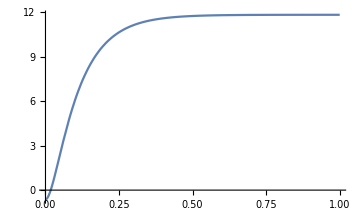
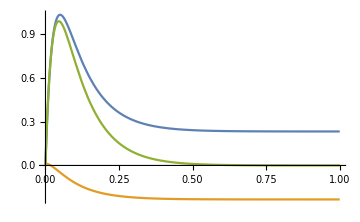

```mathematica
plot2=Plot[{MotorTorque[t,12,0,0,0],ViscousFrictionTorque[t,12,0,0,0],VoltageToTorque[t,12,0,0,0]},{t,0,1},PlotRange->All,ImageSize->Medium];
plot1=Plot[RotationalSpeedAnalytic[t,12,0,0,0],{t,0,1},PlotRange->All,ImageSize->Medium];
{plot1,plot2}
```

#### Braking case

```mathematica
EndMotorTorque=MotorTorque[10,12,0,0,0]
EndViscousTorque=ViscousFrictionTorque[10,12,0,0,0]
EndRotationalSpeed=RotationalSpeedAnalytic[10,12,0,0,0]
EndCurrent=EndMotorTorque/K
```

0.232974

-0.232974

11.8168

0.282436

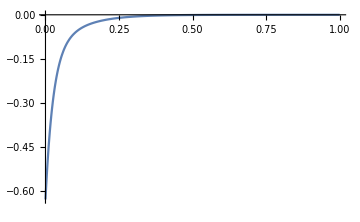
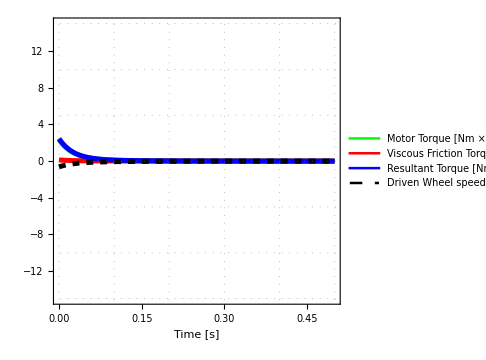

```mathematica
plot1=Plot[RotationalSpeedAnalytic[t,0,0,EndRotationalSpeed,EndCurrent],{t,0,1},PlotRange->All,ImageSize->Medium];
plot2=Plot[{
10 MotorTorque[t,0,0,EndRotationalSpeed,EndCurrent],
10 ViscousFrictionTorque[t,0,0,EndRotationalSpeed,EndCurrent],
10 VoltageToTorque[t,0,0,EndRotationalSpeed,EndCurrent],
RotationalSpeedAnalytic[t,0,0,EndRotationalSpeed,EndCurrent]
},{t,0,0.5},
ImageSize->Medium,
PlotRange->{-15,15},
Frame->True,
PlotLegends->{"Motor Torque [Nm ×10^-1]","Viscous Friction Torque [Nm ×10^-1]","Resultant Torque [Nm ×10^-1]","Driven Wheel speed [rad/s]"},
FrameLabel->{"Time [s]"},
PlotTheme->"Detailed",
LabelStyle->Directive[FontSize->18],
GridLines->{Table[i,{i,0,1,0.1}],Table[i,{i,-15,15,5}]},
GridLinesStyle->Directive[Dotted, Gray],
AspectRatio->1,
PlotStyle->{{Green,Thickness[0.01]},{{Opacity[1],Red},Thickness[0.01]},{Blue,Thickness[0.01]},{Black,Thickness[0.01],Dashed}}];
{plot1,plot2}
```

### DrawAccelerationState

```mathematica
myFontSize=14;
```

```mathematica
DrawAccelerationState[ax_,ay_,ϵz_,MA_,MB_,MC_,nA_,nB_,nC_,UA_,UB_,UC_,cmC_]:={
Opacity[1],
accv=2 wheelCircleRadius {ax,ay,ϵz/10};
axy=N[√(ax^2+ay^2)];
Mv=2 wheelCircleRadius {MA,MB,MC};
Blue,Thickness[vThick],Arrowheads[vArrHead],
	(*Arrow[{rA,rA+Mv⟦1⟧ uyA}],Text["M_A="<>ToString[NumberForm[MA,{6,2}]]<>"[Nm]"<>"\n"<>"n_A="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",rA+wheelCircleRadius uxA],
	Arrow[{rB,rB+Mv⟦2⟧  uyB}],Text["M_B="<>ToString[NumberForm[MB,{6,2}]]<>"[Nm]"<>"\n"<>"n_B="<>ToString[NumberForm[nB,{6,2}]]<>"[N]",rB+wheelCircleRadius uxB],
	Arrow[{rC,rC+Mv⟦3⟧  uyC}],Text["M_C="<>ToString[NumberForm[MC,{6,2}]]<>"[Nm]"<>"\n"<>"n_C="<>ToString[NumberForm[nC,{6,2}]]<>"[N]",rC+wheelCircleRadius uxC],*)
	Arrow[{rA,rA+Mv⟦1⟧ uyA}],Text[Style["U_A="<>ToString[NumberForm[UA,{6,2}]]<>"[V]"<>"\n"<>"n_A="<>ToString[NumberForm[nA,{6,2}]]<>"[N]",FontSize->myFontSize],rA+wheelCircleRadius uxA],
	Arrow[{rB,rB+Mv⟦2⟧  uyB}],Text[Style["U_B="<>ToString[NumberForm[UB,{6,2}]]<>"[V]"<>"\n"<>"n_B="<>ToString[NumberForm[nB,{6,2}]]<>"[N]",FontSize->myFontSize],rB+wheelCircleRadius uxB],
	Arrow[{rC,rC+Mv⟦3⟧  uyC}],Text[Style["U_C="<>ToString[NumberForm[UC,{6,2}]]<>"[V]"<>"\n"<>"n_C="<>ToString[NumberForm[nC,{6,2}]]<>"[N]",FontSize->myFontSize],rC+wheelCircleRadius uxC],
Red,
Thickness[vThick],Arrowheads[vArrHead],
	If[ϵz>0.001,{Arrow[{cmC,cmC+ accv⟦3⟧ uz}],Text[Style["ϵ_z="<>ToString[NumberForm[ϵz,{6,2}]]<>"[s^-2]",FontSize->myFontSize],1.2(cmC+ accv⟦3⟧ uz)]},],
Thickness[vThick],Arrowheads[1.2 vArrHead],
	(*If[ax≠0,{Arrow[{rO,rO+ accv⟦1⟧ ux}],Text["a_x="<>ToString[ax]<>"[m s^-2]",1.2(rO+ accv⟦1⟧ ux)]},],
	If[ay≠0,{Arrow[{rO,rO+ accv⟦2⟧ uy}],Text["a_y="<>ToString[ay]<>"[m s^-2]",1.2(rO+ accv⟦2⟧ uy)]},],*)
If[ay≠0||ax≠0,{Arrow[{cmC,cmC+ accv⟦2⟧ uy+ accv⟦1⟧ ux}],Text[Style["a_xy="<>ToString[NumberForm[axy,{6,2}]]<>"[m s^-2]",FontSize->myFontSize],1.2(cmC+ accv⟦2⟧ uy+ accv⟦1⟧ ux)]},],
};
```

### DrawRobot (dynamic)

```mathematica
textOffset = 0.02;fontSize=16;
RobotGraphics3D[cmC_,rodHeight_,rodHeightPercent_]:=Module[{},{
Gray,Opacity[0.7],
	Sphere[rA,wheelCircleRadius/20],
	Sphere[rB,wheelCircleRadius/20],
	Sphere[rC,wheelCircleRadius/20],
Black,Sphere[cmC,wheelCircleRadius/20],
Gray,Opacity[0.1],
	Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
	Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
	Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],
Black,Thick,Opacity[1],
	(*Line[{wheelCircleRadiusRatio rA,rA}],*)
	Line[{ rA, rA+offsetLength1 uz}],Line[{rA+offsetLength1 uz, rB+offsetLength1 uz}],
	Line[{ rB, rB+offsetLength1 uz}],Line[{rB+offsetLength1 uz, rC+offsetLength1 uz}],
	Line[{ rC, rC+offsetLength1 uz}],Line[{rC+offsetLength1 uz, rA+offsetLength1 uz}],
	Line[{ rA+offsetLength1 uz, rA+offsetLength2 uz}],Line[{rA+offsetLength2 uz, rB+offsetLength2 uz}],
	Line[{ rB+offsetLength1 uz, rB+offsetLength2 uz}],Line[{rB+offsetLength2 uz, rC+offsetLength2 uz}],
	Line[{ rC+offsetLength1 uz, rC+offsetLength2 uz}],Line[{rC+offsetLength2 uz, rA+offsetLength2 uz}],
Black,Opacity[0.2],Triangle[{rA+offsetLength1 uz,rB+offsetLength1 uz,rC+offsetLength1 uz}],
Black,Opacity[0.2],Triangle[{rA+offsetLength2 uz,rB+offsetLength2 uz,rC+offsetLength2 uz}],
(*Cyan,Opacity[0.6],
Cylinder[{r1,r1+dummyCaseHeight uz},dummyCaseRadius],*),
Brown,Opacity[0.2],EdgeForm[White],
(*Cylinder[{r2,r2+packageHeight uz},packageRadius],*)
Cylinder[{r2,r2+rodHeight uz},rodDiameter/2],
Cylinder[{r2+rodHeight rodHeightPercent uz-diskHeight/2 uz,r2+rodHeight rodHeightPercent uz+diskHeight/2 uz},diskDiameter/2]
}];
```

```mathematica
DrawRobot3D[{x_,y_,z_,α_,cmC_,rodHeight_,rodHeightPercent_}]:={EdgeForm[Black],Rotate[Translate[RobotGraphics3D[cmC,rodHeight,rodHeightPercent],{x,y,z}],α,{0,0,1}]}
```

```mathematica
DrawRobot3D2[{x_,y_,z_,α_,cmC_,rodHeight_,rodHeightPercent_}]:={EdgeForm[Black],Rotate[Translate[RobotGraphics3D[cmC,rodHeight,rodHeightPercent],{x,y,z}],α,{1,0,0},rC]}
```

```mathematica
DrawGround={EdgeForm[Black],
planeSize=30 wheelCircleRadius;
Black,Opacity[0.1],Polygon[{{-planeSize wheelCircleRadius,-planeSize wheelCircleRadius,-wheelRadius},{-planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,planeSize wheelCircleRadius,-wheelRadius},{planeSize wheelCircleRadius,-planeSize  wheelCircleRadius,-wheelRadius}}]
};
```

```mathematica
Graphics3D[DrawRobot3D2[{0,0,0,0.7,{0,0,0.3},0.3,1}]~Join~DrawGround,Boxed->False]
```

-Graphics3D-

## Applications

#### Orientation dependence: γ,δ OUT: n_i

```mathematica
Clear[MA,MB,MC];
```

```mathematica
{mOthers,mPackage,mDisk,rodHeight,rodHeightPercent}={0.6,mPackage,1,0.5,1};
inertias=CalculateInertias["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent]
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent]
{UA,UB,UC}=12 A.{ -Sin[γ], Cos[γ], δ};
{MA,MB,MC}={VoltageToTorque[0.05,UA,inertias[[1]],0,0],VoltageToTorque[0.05,UB,inertias[[1]],0,0],VoltageToTorque[0.05,UC,inertias[[1]],0,0]};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

{2.941,{{0.125312,0.,0.},{0.,0.125312,0.},{0.,0.,0.00302106}}}

{0.,0.,0.278388}

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}]//Chop;
solutions//MatrixForm;
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

```mathematica
NA=values[[19]]
NB=values[[20]]
NC=values[[21]]
```

14.7884

14.7884

1.04029

Dangerous orientations

```mathematica
DA=(γ/.FindRoot[D[NA,γ]==0,{γ,2π}])
DB=(γ/.FindRoot[D[NB,γ]==0,{γ,π/4}])
DC=(γ/.FindRoot[D[NC,γ]==0,{γ,π}])
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

γ/.FindRoot[∂_γ NA==0,{γ,2 π}]

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {0.785398}.

ReplaceAll::reps: {FindRoot[∂_γ NB==0,{γ,π/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {0.785398}.

ReplaceAll::reps: {FindRoot[∂_γ NB==0,{γ,π/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

γ/.FindRoot[∂_γ NB==0,{γ,π/4}]

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {3.14159}.

ReplaceAll::reps: {FindRoot[∂_γ NC==0,{γ,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {3.14159}.

ReplaceAll::reps: {FindRoot[∂_γ NC==0,{γ,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

γ/.FindRoot[∂_γ NC==0,{γ,π}]

```mathematica
RobotGraphics3DSimple={
Gray,Opacity[0.1],
	Cylinder[{rA-wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0}),rA+wheelWidth/2 (Normalize[rA][[1;;2]]~Join~{0})},wheelRadius],
	Cylinder[{rB-wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0}),rB+wheelWidth/2 (Normalize[rB][[1;;2]]~Join~{0})},wheelRadius],
	Cylinder[{rC-wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0}),rC+wheelWidth/2 (Normalize[rC][[1;;2]]~Join~{0})},wheelRadius],

Black,Opacity[0.2],Triangle[{rA+offsetLength1 uz,rB+offsetLength1 uz,rC+offsetLength1 uz}],
Opacity[0],White,Cylinder[{{0,0,0},{0,0,0.01}}, 1.5wheelCircleRadius]
};
```

```mathematica
DrawRobot3DSimple[{x_,y_,z_,α_}]:={EdgeForm[Black],Rotate[Translate[RobotGraphics3DSimple,{x,y,z}],α,{0,0,1}]}
```

```mathematica
DrawAccelerationStateSimple[γ_]:={
Opacity[1],
accv= wheelCircleRadius { -Sin[γ],Cos[γ]};
axy=1;
Mv=wheelCircleRadius  A.{ -Sin[γ], Cos[γ], 0};
Blue,Thickness[4 vThick],Arrowheads[4 vArrHead],
	Arrow[{rA,rA+Mv⟦1⟧ uyA}],
	Arrow[{rB,rB+Mv⟦2⟧  uyB}],
	Arrow[{rC,rC+Mv⟦3⟧  uyC}],
Red,
Thickness[4 vThick],Arrowheads[4vArrHead],
If[Cos[γ]≠0||-Sin[γ]≠0,{Arrow[{cmC,cmC+ accv⟦2⟧ uy+ accv⟦1⟧ ux}],},],
};
```

```mathematica
plot1=Plot[{NA,NB,NC},{γ,0,2 π},PlotLegends->"Expressions",PlotRange->{0,30},FrameLabel->{"γ [rad]","Contact Force [N]"},LabelStyle->Directive[FontSize->16],PlotTheme->"Monochrome",Frame->True,GridLines->{Table[i,{i,Pi/4,2 Pi,Pi/4}],Table[i,{i,0,30,1}]},GridLinesStyle->Directive[Dotted, Gray],AspectRatio->1,FrameTicks->{Range[0,2 Pi,Pi/4],Automatic},PlotLegends->Placed[{"N_A","N_B","N_C"},Bottom]];
```

```mathematica
plot2=ListPlot[{{DA,NA/.γ->DA},{DB,NB/.γ->DB},{DC,NC/.γ->DC}},PlotStyle->{Red,PointSize[Large]}];
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

```mathematica
Graphics3D[
DrawRobot3DSimple[initialPos]~Join~DrawAccelerationStateSimple[DA],Boxed->False,ViewPoint->Above,ImageSize->250];
Graphics3D[
DrawRobot3DSimple[initialPos]~Join~DrawAccelerationStateSimple[DB],Boxed->False,ViewPoint->Above,ImageSize->250];
Graphics3D[
DrawRobot3DSimple[initialPos]~Join~DrawAccelerationStateSimple[DC],Boxed->False,ViewPoint->Above,ImageSize->250];
```

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {6.28319}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_γ NA==0,{γ,2 π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {0.785398}.

ReplaceAll::reps: {FindRoot[∂_γ NB==0,{γ,π/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {0.785398}.

ReplaceAll::reps: {FindRoot[∂_γ NB==0,{γ,π/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {0.785398}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_γ NB==0,{γ,π/4}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {3.14159}.

ReplaceAll::reps: {FindRoot[∂_γ NC==0,{γ,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {3.14159}.

ReplaceAll::reps: {FindRoot[∂_γ NC==0,{γ,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {True} is not a list of numbers with dimensions {1} at {γ} = {3.14159}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_γ NC==0,{γ,π}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

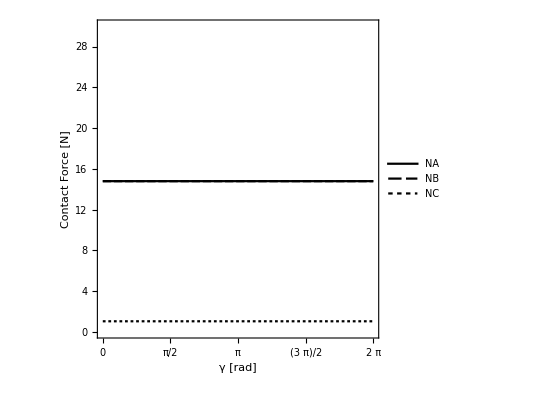

```mathematica
Show[plot1,plot2]
```

#### Accelerating case solution

```mathematica
{mOthers,mPackage,mDisk,rodHeight,rodHeightPercent}={0.4,mPackage,1,1,1};
inertias=CalculateInertias["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=0;
initialCurrent=0;
{UA,UB,UC}=12 A.{0,-1,0×1/wheelCircleRadius};{UA,UB,UC}={-12,12,0};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]];
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]];
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UC,atMass,initialSpeed,initialCurrent]
};
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//Chop//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]~Join~solutions[[31;;33]]//MatrixForm//Chop
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions//Chop;
```

(ax→0
ay→-2.34689
ϵz→0
nA→18.5871
nB→18.5871
nC→-8.51924
ϵAx→67.7488
ϵBx→-67.7488
ϵCx→0)

```mathematica
Graphics3D[
DrawRobot3D[initialPos~Join~{currentCOM,rodHeight,rodHeightPercent}]~Join~DrawGround~Join~DrawAccelerationState[values⟦1⟧,values⟦2⟧,values⟦6⟧,MA,MB,MC,values⟦19⟧,values⟦20⟧,values⟦21⟧,UA,UB,UC,currentCOM],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False,ImageSize->Large]
```

-Graphics3D-

#### Braking case solution

```mathematica
{mOthers,mPackage,mDisk,rodHeight,rodHeightPercent}={0.4,mPackage,1,1,1};
inertias=CalculateInertias["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=RotationalSpeedAnalytic[10,12,0,0,0];
initialCurrent=ArmatureCurrentAnalytic[10,12,0,0,0];
{UA,UB,UC}=12 A.{0,0,0×1/wheelCircleRadius};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]];
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]];
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,-initialSpeed,-initialCurrent],
VoltageToTorque[atTime,UC,atMass,0,0]
};
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//Chop//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]~Join~solutions[[31;;33]]//MatrixForm//Chop
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions//Chop;
```

(ax→0
ay→-2.34689
ϵz→0
nA→18.5871
nB→18.5871
nC→-8.51924
ϵAx→67.7488
ϵBx→-67.7488
ϵCx→0)

```mathematica
Graphics3D[
DrawRobot3D[initialPos~Join~{currentCOM,rodHeight,rodHeightPercent}]~Join~DrawGround~Join~DrawAccelerationState[values⟦1⟧,values⟦2⟧,values⟦6⟧,MA,MB,MC,values⟦19⟧,values⟦20⟧,values⟦21⟧,UA,UB,UC,currentCOM],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False,ImageSize->Large]
```

-Graphics3D-

#### Braking (time integration)

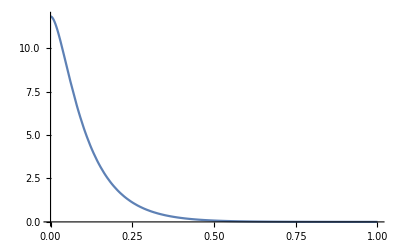
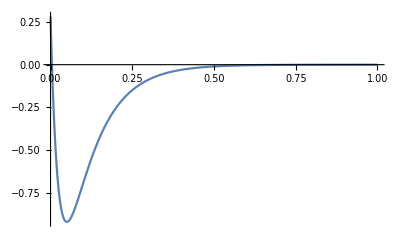
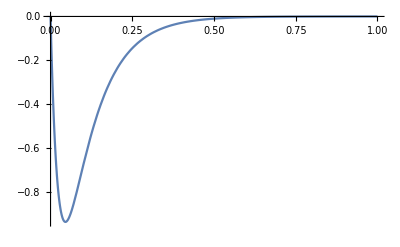

```mathematica
h=0.005;n=150;
{mOthers,mPackage,mDisk,rodHeight,rodHeightPercent}={0.4,2,1,1,1};
inertias=CalculateInertias["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
stationaryNormalLoad=inertias[[1]]*g/3;
initialVoltage =12;initialTime=0.00;
initialSpeed=RotationalSpeedAnalytic[10,initialVoltage,0,0,0];
initialCurrent=ArmatureCurrentAnalytic[10,initialVoltage,0,0,0];
initialTorque=VoltageToTorque[10,initialVoltage,0,0,0];
atTime=peakTime;
atMass=0;
peakTorque=FindMinimum[VoltageToTorque[T,0,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]];
peakTime=T/.FindMinimum[VoltageToTorque[T,0,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]];
plot1=Plot[RotationalSpeedAnalytic[t,0,0,initialSpeed,initialCurrent],{t,0,1},PlotRange->All];
plot2=Plot[ArmatureCurrentAnalytic[t,0,0,initialSpeed,initialCurrent],{t,0,1},PlotRange->All];
plot3=Plot[VoltageToTorque[t,0,0,initialSpeed,initialCurrent],{t,0,1},PlotRange->All];
{plot1,plot2,plot3}
```

```mathematica
CalculateNextTimeStep[{time_,NA_,NB_,NC_,speed_,current_,voltage_,torque_}]:=Module[{newTime,newNA,newNB,newNC,newspeed,newcurrent,newvoltage,newtorque},
inertias=CalculateInertias["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
{UA,UB,UC}=12 A.{0,0,0×1/wheelCircleRadius};
newTime=time+h;
newvoltage=0×voltage(1-10 h);
{MA,MB,MC}={
MotorTorque[newTime,newvoltage,atMass,initialSpeed,initialCurrent]-b speed,
MotorTorque[newTime,-newvoltage,atMass,-initialSpeed,-initialCurrent]-b speed,
MotorTorque[newTime,0,atMass,0,0]
};
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//FullSimplify//N;
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
newNA=nA/.solutions[[16]];
newNB=nB/.solutions[[17]];
newNC=nC/.solutions[[18]];
newspeed=speed-h×ϵA[[1]]/.solutions;
(*newspeed=RotationalSpeedAnalytic[newTime,newvoltage,atMass,speed,current]*);
newcurrent=ArmatureCurrentAnalytic[newTime,newvoltage,atMass,speed,current];
newtorque=VoltageToTorque[newTime,newvoltage,atMass,initialSpeed,initialCurrent];
{newTime,newNA,newNB,newNC,newspeed,newcurrent,newvoltage,newtorque}
]
```

```mathematica
initializationVector={initialTime,stationaryNormalLoad,stationaryNormalLoad,stationaryNormalLoad,initialSpeed,initialCurrent,initialVoltage,initialTorque};
CalculateNextTimeStep[initializationVector];
```

```mathematica
Motion=NestList[CalculateNextTimeStep,initializationVector,n+1];
```

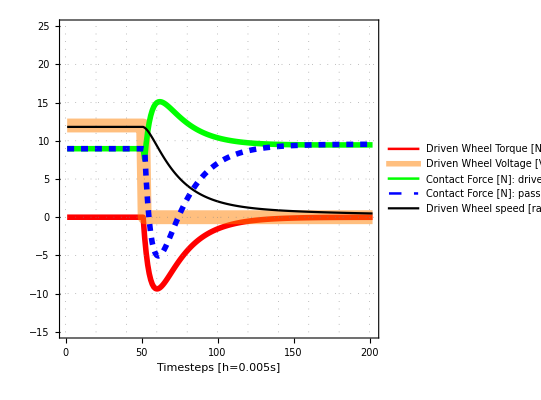

```mathematica
skip=1;precedingValues=50;
contactForceFront=Table[stationaryNormalLoad,{i,1,precedingValues}]~Join~Motion[[skip;; ;;skip,2]];
contactForceRear=Table[stationaryNormalLoad,{i,1,precedingValues}]~Join~Motion[[skip;; ;;skip,4]];
drivenWheelSpeed=Table[initialSpeed,{i,1,precedingValues}]~Join~Motion[[skip;; ;;skip,5]];
brakingVoltage=Table[initialVoltage,{i,1,precedingValues}]~Join~Motion[[skip;; ;;skip,7]];
brakingTorque=Table[initialTorque,{i,1,precedingValues}]~Join~Motion[[skip;; ;;skip,8]];
ListLinePlot[{10 brakingTorque,brakingVoltage,contactForceFront,contactForceRear,drivenWheelSpeed},
PlotRange->{-15,25},
Frame->True,
PlotLegends->{"Driven Wheel Torque [Nm ×10^-1]","Driven Wheel Voltage [V]","Contact Force [N]: driven","Contact Force [N]: passive","Driven Wheel speed [rad/s]"},
FrameLabel->{"Timesteps [h=0.005s]"},
PlotTheme->"Detailed",
LabelStyle->Directive[FontSize->18],
GridLines->{Table[i,{i,0,200,20}],Table[i,{i,-10,20,5}]},
GridLinesStyle->Directive[Dotted, Gray],
AspectRatio->1,
PlotStyle->{{Red,Thickness[0.01]},{{Opacity[0.5],Orange},Thickness[0.025]},{Green,Thickness[0.01]},{Blue,Thickness[0.01],Dashed},{Black}}]
```

#### Effect of mass on acceleration

```mathematica
inertias=CalculateInertias["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent]
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDisk,rodHeight,rodHeightPercent];
g=9.81;v=0 v;ω=0 ω;
vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=RotationalSpeedAnalytic[10,12,0,0,0];
initialCurrent=ArmatureCurrentAnalytic[10,12,0,0,0];
{UA,UB,UC}=12 A.{0,0,0×1/wheelCircleRadius};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]]
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]]
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,-initialSpeed,-initialCurrent],
VoltageToTorque[atTime,UC,atMass,0,0]
}
eq1SUBS=eq1/.mRobot->inertias[[1]]+X;
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

{2.741,{{0.448924,0.,0.},{0.,0.448924,0.},{0.,0.,0.00302106}}}

-0.938475

0.0456248

{-0.938475,0.938475,0.}

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]//MatrixForm;
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

```mathematica
aYFunctionOfMass=ay/.solutions[[2]]
```

-(8.84048×10^-17+3.82918×10^-18 X)/(3.76689×10^-17+3.2632×10^-18 X+7.06714×10^-20 X^2)

```mathematica
nFunctionOfMass=nC/.solutions[[18]]
```

-(3.20911×10^-16+1.23482×10^-16 X-5.88854×10^-19 X^2-2.31095×10^-19 X^3)/(3.76689×10^-17+3.2632×10^-18 X+7.06714×10^-20 X^2)

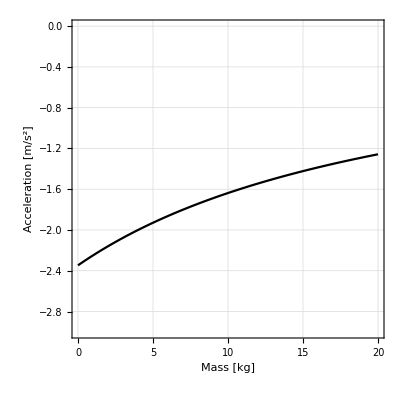

```mathematica
Plot[aYFunctionOfMass,{X,0,20},PlotRange->{-3,0},PlotTheme->"Monochrome",FrameLabel->{"Mass [kg]","Acceleration [m/s^2]"},LabelStyle->{FontSize->14},Frame->True,GridLines->Automatic,AspectRatio->1]
```

#### Effect of disk mass on contact force

```mathematica
inertias=CalculateInertias["Disk",mOthers,mPackage,X,rodHeight,rodHeightPercent];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,X,rodHeight,rodHeightPercent];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=0;
initialCurrent=0;
{UA,UB,UC}=12 A.{0,-1,0×1/wheelCircleRadius};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]]
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]]
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UC,atMass,initialSpeed,initialCurrent]
}
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

-0.812743

0.0456248

{-0.812743,0.812743,0.}

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]//MatrixForm
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(ax→-(8.12141×10^-115-2.53794×10^-116 X^2)/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(KAx (2.03035×10^-115-1.58621×10^-117 X^2+2.47846×10^-119 X^3))/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))
ay→-(3.56037×10^-115+2.01459×10^-115 X+8.39128×10^-117 X^2-1.98118×10^-132 X^3)/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(KAx (1.80332×10^-130+1.52155×10^-130 X+1.46167×10^-131 X^2+3.79727×10^-133 X^3))/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))
ϵz→-(KAx (-2.03035×10^-115 X-1.26897×10^-116 X^2-1.98277×10^-118 X^3))/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(3.24857×10^-114-1.62428×10^-114 X+1.01518×10^-115 X^2+3.17243×10^-117 X^3)/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))
nB→-(KAx (-6.49713×10^-114-3.24857×10^-114 X^2+3.17243×10^-117 X^4))/((-8.25016×10^-45-4.29472×10^-45 X) (1.741+X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(-1.29943×10^-113-1.03954×10^-112 X-6.49713×10^-114 X^3-1.52277×10^-115 X^4-5.84767×10^-118 X^5)/((-8.25016×10^-45-4.29472×10^-45 X) (1.741+X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))
nC→-(KAx (-4.95912×10^-130-2.52464×10^-129 X-1.98365×10^-129 X^2-4.84641×10^-130 X^3-1.83149×10^-131 X^4))/((-8.25016×10^-45-4.29472×10^-45 X) (1.741+X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(-8.13508×10^-115+1.78895×10^-114 X+2.77067×10^-114 X^2+8.8665×10^-115 X^3+2.17175×10^-116 X^4-5.84767×10^-118 X^5)/((-8.25016×10^-45-4.29472×10^-45 X) (1.741+X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))
sA→-(-5.07588×10^-116+4.95692×10^-119 X^3)/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(KAx (3.29932×10^-115+2.06208×10^-115 X+1.6457×10^-116 X^2+3.56278×10^-118 X^3))/((-8.25016×10^-45-4.29472×10^-45 X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2)))

```mathematica
aYFunctionOfDiskMass=ay/.solutions[[2]]/.KAx->1;
```

```mathematica
nFunctionOfDiskMass=nC/.solutions[[17]]/.KAx->1
```

-(-4.95912×10^-130-2.52464×10^-129 X-1.98365×10^-129 X^2-4.84641×10^-130 X^3-1.83149×10^-131 X^4)/((-8.25016×10^-45-4.29472×10^-45 X) (1.741+X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))-(-8.13508×10^-115+1.78895×10^-114 X+2.77067×10^-114 X^2+8.8665×10^-115 X^3+2.17175×10^-116 X^4-5.84767×10^-118 X^5)/((-8.25016×10^-45-4.29472×10^-45 X) (1.741+X) (-2.03132×10^-71-1.83937×10^-72 X-4.1639×10^-74 X^2))

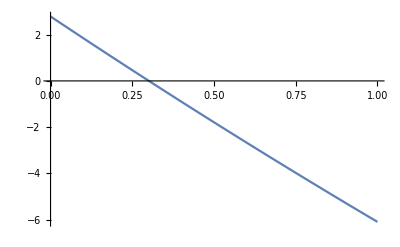

```mathematica
Plot[nFunctionOfDiskMass,{X,0,1},PlotRange->Full]
```

#### Effect of rod height percent on contact force

```mathematica
inertias=CalculateInertias["Disk",mOthers,mPackage,0.5,rodHeight,X];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,0.5,rodHeight,X];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=0;
initialCurrent=0;
{UA,UB,UC}=12 A.{0,-1,0×1/wheelCircleRadius};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]]
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]]
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UC,atMass,initialSpeed,initialCurrent]
}
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

-0.812743

0.0456248

{-0.812743,0.812743,0.}

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]//MatrixForm
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

(ax→1.20087×10^-16
ay→-2.07746
ϵz→-5.9952×10^-14
nA→9.88443+2.88536 X
nB→9.88443+2.88536 X
nC→3.98116-5.77071 X)

```mathematica
aYFunctionOfDiskMass=ay/.solutions[[2]]/.KAx->1;
```

```mathematica
nFunctionOfRodHeightPercent=nC/.solutions[[18]]
```

3.98116-5.77071 X

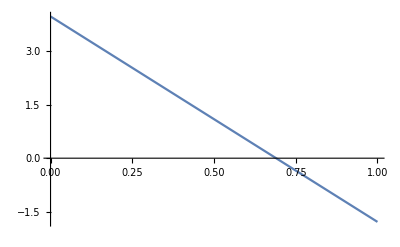

```mathematica
Plot[nFunctionOfRodHeightPercent,{X,0,1},PlotRange->Full]
```

#### Effect of rod height on contact force

```mathematica
inertias=CalculateInertias["Disk",mOthers,mPackage,0.5,X,rodHeightPercent];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,0.5,X,rodHeightPercent];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=0;
initialCurrent=0;
{UA,UB,UC}=12 A.{0,-1,0×1/wheelCircleRadius};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]]
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]]
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UC,atMass,initialSpeed,initialCurrent]
}
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

-0.812743

0.0456248

{-0.812743,0.812743,0.}

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]//MatrixForm
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

(ax→1.20087×10^-16
ay→-2.07746
ϵz→-5.9952×10^-14
nA→8.80819+3.96159 X
nB→8.80819+3.96159 X
nC→6.13364-7.92319 X)

```mathematica
aYFunctionOfDiskMass=ay/.solutions[[2]]/.KAx->1;
```

```mathematica
nFunctionOfRodHeight=nC/.solutions[[18]]
```

6.13364-7.92319 X

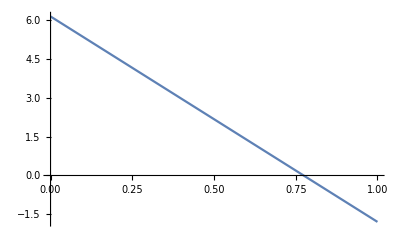

```mathematica
Plot[nFunctionOfRodHeight,{X,0,1},PlotRange->Full]
```

#### Effect of rod height percent on contact force

```mathematica
inertias=CalculateInertias["Disk",mOthers,mPackage,X,rodHeight,Y];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,X,rodHeight,Y];
g=9.81;v=0 v;ω=0 ω;
vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{UA,UB,UC}=12 A.{0,-1,0×1/wheelCircleRadius};
{MA,MB,MC}={VoltageToTorque[0.05,UA,0,0,coeff],VoltageToTorque[0.05,UB,0,0,coeff],VoltageToTorque[0.05,UC,0,0,coeff]};
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
```

```mathematica
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//FullSimplify//N;
```

```mathematica
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
solutions[[1;;2]]~Join~{solutions[[6]]}~Join~solutions[[16;;18]]//MatrixForm
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions;
```

Solve::svars: Equations may not give solutions for all "solve" variables.

(ax→-(8.12141×10^-115)/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(KAx (1.58621×10^-117 X^2+2.47846×10^-119 X^3))/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))
ay→-(3.53707×10^-115+2.00625×10^-115 X+8.36002×10^-117 X^2-1.93716×10^-132 X^3)/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(KAx (2.25415×10^-130+1.46519×10^-130 X+1.44406×10^-131 X^2+3.79727×10^-133 X^3))/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))
ϵz→-(KAx (-1.26897×10^-116 X^2-1.98277×10^-118 X^3))/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(3.24857×10^-114+1.01518×10^-115 X^2+3.17243×10^-117 X^3)/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))
nB→-(-2.59885×10^-113-1.29943×10^-113 X-6.49713×10^-114 X^2-8.12141×10^-115 X^3-4.4414×10^-116 X^4-5.84767×10^-118 X^5-5.1977×10^-113 X^2 Y-5.07588×10^-116 X^4 Y)/((-8.22869×10^-45-4.29472×10^-45 X) (1.736+X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(KAx (2.53794×10^-116 X^3+1.98277×10^-118 X^4-3.17243×10^-117 X^4 Y))/((-8.22869×10^-45-4.29472×10^-45 X) (1.736+X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))
nC→-(KAx (-3.60663×10^-130-5.86078×10^-130 X-2.70497×10^-130 X^2-4.36741×10^-131 X^3-1.51891×10^-132 X^4-1.62298×10^-129 X Y-1.62298×10^-129 X^2 Y-4.39558×10^-130 X^3 Y-1.65539×10^-131 X^4 Y))/((-8.22869×10^-45-4.29472×10^-45 X) (1.736+X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(-8.09716×10^-115-1.64942×10^-114 X-1.15403×10^-114 X^2-3.13693×10^-115 X^3-2.49018×10^-116 X^4-5.84767×10^-118 X^5+3.41131×10^-114 X Y+3.89995×10^-114 X^2 Y+1.19521×10^-114 X^3 Y+4.64446×10^-116 X^4 Y)/((-8.22869×10^-45-4.29472×10^-45 X) (1.736+X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))
sA→-(-5.07588×10^-116-3.17243×10^-117 X^2-4.95692×10^-119 X^3)/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(KAx (3.29932×10^-115+2.03035×10^-115 X+1.6457×10^-116 X^2+3.56278×10^-118 X^3))/((-8.22869×10^-45-4.29472×10^-45 X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2)))

```mathematica
aYFunctionOfDiskMass=ay/.solutions[[2]]/.KAx->1;
```

```mathematica
nFunctionOfRodHeightPercentDiskWeight=nC/.solutions[[17]]/.KAx->1
```

-(-3.60663×10^-130-5.86078×10^-130 X-2.70497×10^-130 X^2-4.36741×10^-131 X^3-1.51891×10^-132 X^4-1.62298×10^-129 X Y-1.62298×10^-129 X^2 Y-4.39558×10^-130 X^3 Y-1.65539×10^-131 X^4 Y)/((-8.22869×10^-45-4.29472×10^-45 X) (1.736+X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))-(-8.09716×10^-115-1.64942×10^-114 X-1.15403×10^-114 X^2-3.13693×10^-115 X^3-2.49018×10^-116 X^4-5.84767×10^-118 X^5+3.41131×10^-114 X Y+3.89995×10^-114 X^2 Y+1.19521×10^-114 X^3 Y+4.64446×10^-116 X^4 Y)/((-8.22869×10^-45-4.29472×10^-45 X) (1.736+X) (-2.0304×10^-71-1.83896×10^-72 X-4.1639×10^-74 X^2))

```mathematica
Plot3D[{nFunctionOfRodHeightPercentDiskWeight},{X,0,1},{Y,0,1},PlotPoints->100,MaxRecursion->6,PlotRange->{{0,1},{0,1},{-15,10}},AxesLabel->{"Disk Mass [kg]","Disk CoM, Z coord [m]","Contact Force [N]"},Boxed->True,LabelStyle->{FontSize->14},ColorFunction->Function[{x,y,z},RGBColor[If[z>0.75,1,1],If[z>0.75,0,1],If[z>0.75,0,1]]]]
```

-Graphics3D-

#### Parametric Robot

```mathematica
Clear[mDisk,rodHeight,rodHeightPercent]
```

```mathematica
Manipulate[
inertias=CalculateInertias["Disk",mOthers,mPackage,mDiskPAR,rodHeightPAR,rodHeightPercentagePAR];
currentCOM=CommonCenterOfMassCalc["Disk",mOthers,mPackage,mDiskPAR,rodHeightPAR,rodHeightPercentagePAR];
g=9.81;v=0 v;ω=0 ω;vA=0 vA;ωA=0 ωA;vB=0 vB;ωB=0 ωB;vC=0 vC;ωC=0 ωC;
{ωx,ωy,ωz}={0,0,0};{ωAx,ωAy,ωAz}={0,0,0};{ωBx,ωBy,ωBz}={0,0,0};{ωCx,ωCy,ωCz}={0,0,0};
initialSpeed=0;
initialCurrent=0;
{UA,UB,UC}=12 A.{0,-1,0×1/wheelCircleRadius};
peakTorque=FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[1]];
peakTime=T/.FindMinimum[VoltageToTorque[T,UA,atMass,initialSpeed,initialCurrent],{T,0.1}][[2]];
atTime=peakTime;
atMass=0;
{MA,MB,MC}={
VoltageToTorque[atTime,UA,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UB,atMass,initialSpeed,initialCurrent],
VoltageToTorque[atTime,UC,atMass,initialSpeed,initialCurrent]
};
eq1SUBS=eq1/.mRobot->inertias[[1]];
eq2SUBS=eq2/.θRobot->inertias[[2]]/.cmCX->currentCOM[[1]]/.cmCY->currentCOM[[2]]/.cmCZ->currentCOM[[3]];
{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ}//Column//Chop//FullSimplify//N;
solutions=First@Solve[{eq1SUBS,eq2SUBS,eq1A,eq1B,eq1C,eq2A,eq2B,eq2C,rigidBodyA,rigidBodyB,rigidBodyC,rollingY,rollingZ},{ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,nA,nB,nC,sA,sB,sC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}];
values={ax,ay,az,ϵx,ϵy,ϵz,KAx,KBx,KCx,KAy,KBy,KCy,KAz,KBz,KCz,sA,sB,sC,nA,nB,nC,aAx,aAy,aAz,aBx,aBy,aBz,aCx,aCy,aCz,ϵAx,ϵBx,ϵCx,ϵAy,ϵBy,ϵCy,ϵAz,ϵBz,ϵCz}/.solutions//Chop;
GraphicsRow[{
Graphics3D[
DrawRobot3D[initialPos~Join~{currentCOM,rodHeightPAR,rodHeightPercentagePAR}]~Join~DrawGround~Join~DrawAccelerationState[values⟦1⟧,values⟦2⟧,values⟦6⟧,MA,MB,MC,values⟦19⟧,values⟦20⟧,values⟦21⟧,UA,UB,UC,currentCOM],
AxesLabel->{x,y,z},Axes->{False, False, False},Boxed->False,ImageSize->Large
],
Text[Style["CoM = "<>ToString[NumberForm[currentCOM,{6,4}]]"\n",FontSize->16]]
},ImageSize->1300],
{{VoltageAmplitude,12},-12,12},
{{mDiskPAR,0.5},0,2},
{{rodHeightPAR,1},0,1},
{{rodHeightPercentagePAR,0.5},0,1}]
```